Solving Initial Value Problem With Mathematica...

```mathematica
q[t_]= A ⅇ^(-α t) Cos[β t + ϕ]
```

A ⅇ^(-t α) Cos[t β+ϕ]

```mathematica
first=D[q[t], t]
```

-A ⅇ^(-t α) α Cos[t β+ϕ]-A ⅇ^(-t α) β Sin[t β+ϕ]

```mathematica
second=D[q[t], {t,2}]
```

A ⅇ^(-t α) α^2 Cos[t β+ϕ]-A ⅇ^(-t α) β^2 Cos[t β+ϕ]+2 A ⅇ^(-t α) α β Sin[t β+ϕ]

```mathematica
equation = second-(-γ q[t] - first)
```

-A ⅇ^(-t α) α Cos[t β+ϕ]+A ⅇ^(-t α) α^2 Cos[t β+ϕ]-A ⅇ^(-t α) β^2 Cos[t β+ϕ]+A ⅇ^(-t α) γ Cos[t β+ϕ]-A ⅇ^(-t α) β Sin[t β+ϕ]+2 A ⅇ^(-t α) α β Sin[t β+ϕ]

```mathematica
Coefficient[equation, Cos[β t+ ϕ]]
```

-A ⅇ^(-t α) α+A ⅇ^(-t α) α^2-A ⅇ^(-t α) β^2+A ⅇ^(-t α) γ

```mathematica
CosCoeff = Coefficient[equation, Cos[β t+ ϕ]]/(A ⅇ^(-α t))//Simplify
```

-α+α^2-β^2+γ

```mathematica
SinCoeff =Coefficient[equation, Sin[β t+ ϕ]]/(A ⅇ^(-α t))//Simplify
```

(-1+2 α) β

```mathematica
sol = Solve[{CosCoeff ==0, SinCoeff ==0}, {α, β}]
```

{{α→1/2,β→-1/2 √(-1+4 γ)},{α→1/2,β→1/2 √(-1+4 γ)},{α→1/2 (1-√(1-4 γ)),β→0},{α→1/2 (1+√(1-4 γ)),β→0}}

Under Damped Case :- 
When Beta is real, and non-zero. 
Alpha is 1/2 and Beta is just a difference of phi. Which gives, only the difference in changing the sign of Phi [See the equations above] 
   
Critical Damped Case:- 
When Frequency becomes zero, damped constant becomes equal to natural frequency, or beta becomes zero.  All four solutions become identical to each other in critical damping.

```mathematica
sol[[1]]
```

{α→1/2,β→-1/2 √(-1+4 γ)}

```mathematica
sol[[2]]
```

{α→1/2,β→1/2 √(-1+4 γ)}

```mathematica
qsol[t_]= q[t]/. {α->1/2,β->1/2 √(-1+4 γ)}
```

A ⅇ^(-t/2) Cos[1/2 t √(-1+4 γ)+ϕ]

```mathematica
qso'[t]=D[qsol[t], t]/.t->0
```

-1/2 A Cos[ϕ]-1/2 A √(-1+4 γ) Sin[ϕ]

```mathematica
bcsol = Solve[{qsol[0] ==1, qso'[t] ==0}, {A, ϕ}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{A→-(2 √γ)/(√(-1+4 γ)),ϕ→-ArcCos[-(√(-1+4 γ))/(2 √γ)]},{A→-(2 √γ)/(√(-1+4 γ)),ϕ→ArcCos[-(√(-1+4 γ))/(2 √γ)]},{A→(2 √γ)/(√(-1+4 γ)),ϕ→-ArcCos[(√(-1+4 γ))/(2 √γ)]},{A→(2 √γ)/(√(-1+4 γ)),ϕ→ArcCos[(√(-1+4 γ))/(2 √γ)]}}

```mathematica
qfinal[γ_, t_]= qsol[t]/. bcsol[[4]]
```

(2 ⅇ^(-t/2) √γ Cos[1/2 t √(-1+4 γ)+ArcCos[(√(-1+4 γ))/(2 √γ)]])/(√(-1+4 γ))

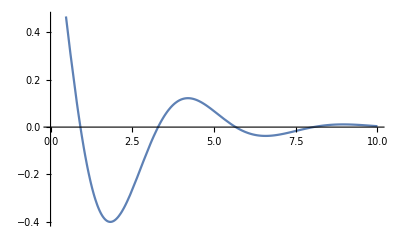

```mathematica
Plot[qfinal[t], {t,0,10}]
```

```mathematica
Manipulate[Plot[qfinal[γ, t], {t,0,10}, PlotStyle->Gray, PlotRange->All], {γ, 1/4 + 0.01, 4}]
```

Small Value of Gamma means, that Damping is dominant, and Large value of gamma means that, other term is dominant.

Damped Harmonic Oscillator in Spring Mass-System...

mx’’[t] = -2k x[t]

From here, comes Oscillation Time Scales. 

m x’’[t] = -2k x[t] - μ mg Sgn[x]

From other term, comes the Damping time Scales. 

Physical Scales :-  Mass, Spring constant and μg , a or a_0 are all Physical scales
Time Scales :-  Oscillation and Daming Time Scales. 

Oscillation -> 2π √(m/(2k))
Damping -> 2π √(a_0/μg) [It came like, Dividing acceleration, by Length Scale, and then taking its square root.

```mathematica
NDSolve[{z''[t] == -z[t] - 0.02 Sign[z'[t]], z'[0]==0, z[0]==1}, z[t], {t, 0, 100}]
```

NDSolve::deqn: Equation or list of equations expected instead of True in the first argument {True,z'[0]==0,z[0]==1}.

NDSolve[{True,z'[0]==0,z[0]==1},z[t],{t,0,100}]

```mathematica
numsol = NDSolve[{z''[t] == -z[t] - 0.02 Sign[z'[t]], z'[0]==0, z[0]==1}, z[t], {t, 0, 100}]
```

NDSolve::deqn: Equation or list of equations expected instead of True in the first argument {True,z'[0]==0,z[0]==1}.

NDSolve[{True,z'[0]==0,z[0]==1},z[t],{t,0,100}]

Paste this Online, It will Work there.

```mathematica
Plot[z[t]/.numsol, {t,0,100}]
```

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{True,z'[0]==0,z[0]==1},z[0.00204286],{0.00204286,0,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{True,z'[0.]==0.,z[0.]==1.},z[0.00204286],{0.00204286,0.,100.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 2.04286 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{True,z'[0]==0,z[0]==1},z[2.04286],{2.04286,0,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

Dimensional analysis is not so correct like Physics of Damping.

Introduction to Euler’s method for solving Differentials Equation...

Just Edit this Code for whatsoever the function is being given to You. Be Happy.

```mathematica
g[t_,y_]= 4t + 3 y
```

4 t+3 y

```mathematica
g[1,2]
```

10

```mathematica
yi=1;
ti=0;
tf=15;
nMax=50;
h=(tf-ti)/nMax;
```

```mathematica
data={};

yprev=yi;

tprev=ti;

data=Append[data,{tprev,yprev}];
```

```mathematica
For[n=1,n<=nMax,n++,
ynext=yprev+h g[tprev,yprev];
tnext=tprev+h;
data=Append[data,{tnext,ynext}];
yprev=ynext;
tprev=tnext;
]
```

```mathematica
data//N
```

{{0.,1.},{0.3,1.9},{0.6,3.97},{0.9,8.263},{1.2,16.7797},{1.5,33.3214},{1.8,65.1107},{2.1,125.87},{2.4,241.674},{2.7,462.06},{3.,881.154},{3.3,1677.79},{3.6,3191.77},{3.9,6068.68},{4.2,11535.2},{4.5,21921.9},{4.8,41656.9},{5.1,79153.9},{5.4,150399.},{5.7,285764.},{6.,542958.},{6.3,1.03163×10^6},{6.6,1.9601×10^6},{6.9,3.7242×10^6},{7.2,7.07598×10^6},{7.5,1.34444×10^7},{7.8,2.55443×10^7},{8.1,4.85342×10^7},{8.4,9.2215×10^7},{8.7,1.75209×10^8},{9.,3.32896×10^8},{9.3,6.32503×10^8},{9.6,1.20176×10^9},{9.9,2.28334×10^9},{10.2,4.33834×10^9},{10.5,8.24284×10^9},{10.8,1.56614×10^10},{11.1,2.97567×10^10},{11.4,5.65376×10^10},{11.7,1.07422×10^11},{12.,2.04101×10^11},{12.3,3.87792×10^11},{12.6,7.36804×10^11},{12.9,1.39993×10^12},{13.2,2.65986×10^12},{13.5,5.05374×10^12},{13.8,9.60211×10^12},{14.1,1.8244×10^13},{14.4,3.46636×10^13},{14.7,6.58608×10^13},{15.,1.25136×10^14}}

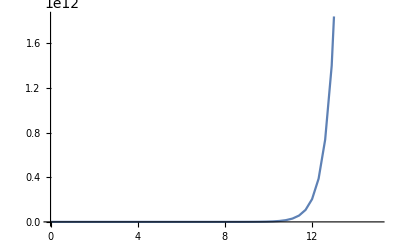

```mathematica
Plot1=ListPlot[data,Joined->True]
```

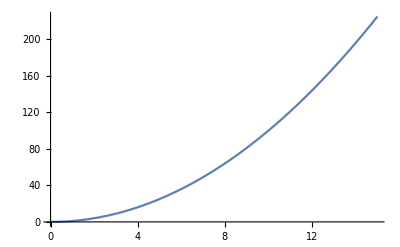

```mathematica
Plot2=Plot[t^2 ,{t,ti,tf}]
```

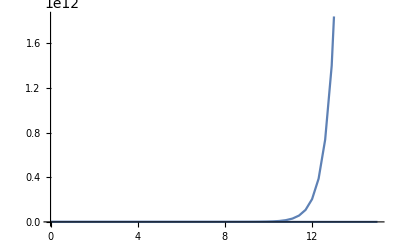

```mathematica
Show[Plot1,Plot2]
```